# Skeleton-based Analysis of Melt Network

## Functions

```mathematica
Clear["Global`*"];
```

readSkel[path] reads .ply skeleton file as a table and returns points, lines and radius:

```mathematica
readSkel:= Function[path, 
	rawData = Import[path,"Table"];
	numOfPoints = rawData⟦3,3⟧;
	numOfEdges = rawData⟦9,3⟧;
	dataTable = rawData⟦15;;,;;⟧;
	
	Points = dataTable⟦;;numOfPoints,3;;5⟧;
	Lines = dataTable⟦numOfPoints+1;;⟧ + 1;
	Radius = dataTable⟦;;numOfPoints,2⟧;
	{Points,Lines,Radius}
]
```

getRange[list] returns the range(min and max value) of elements in the list:

```mathematica
getRange:=Function[list,
	min = Min[list];
	max = Max[list];
	{min, max}]
```

move[from, to] add an offset to list from based on the distance between center of range2 and range1:

```mathematica
move:=Function[{from,to},
	range1 = getRange[from];
	range2 = getRange[to];
	offset = (range2⟦1⟧ + range2⟦2⟧-range1⟦1⟧ - range1⟦2⟧)/2;
	res = from + offset;
	res]
```

coordsAlign[coords1, coords2] add offsets to each dimension of coords1 so that coords1 is aligned with coords2. coords1, coords2: N by 3(x,y,z)

```mathematica
coordsAlign:=Function[{coords1,coords2},
	newX = move[coords1⟦;;,1⟧,coords2⟦;;,1⟧];
	newY = move[coords1⟦;;,2⟧,coords2⟦;;,2⟧];
	newZ = move[coords1⟦;;,3⟧,coords2⟦;;,3⟧];
	newCoords1 = {newX,newY,newZ};
	Transpose[newCoords1]]
```

linesToGraph[lines] construct a graph based on the lines

```mathematica
linesToGraph:=Function[{lines},
	graph=Graph[Table[lines⟦i,1⟧<->lines⟦i,2⟧,{i,1,Dimensions[lines]⟦1⟧}]]
]
```

getJunctions[graph] collect all junction nodes(degree >= 3) and their degree from a graph

```mathematica
getJunctions:=Function[{graph},
	ans={};
	For[i=1,i≤VertexCount[graph],i++,
	degree = VertexDegree[graph,i];
	If[degree>2,AppendTo[ans,{i,degree}]]];
	ans
]
```

InitJG[points, lines, radius] generates a list of junctions and a simplified graph based on these junctions
	Inputs: 
		points: a list of all points in skeleton
		lines: a list of all lines in skeleton
		radius: a list of radius of each point in skeleton
	Returns:
		junctionDataTable: a list of all basic junctions {identifier, degree, cluster, coordinate, radius}
		simplifiedG: a simplified graph which eliminates all vertices with degree of 2

```mathematica
initJG:= Function[{points, lines, radius},
	skelGraph = linesToGraph[lines];
	Print["Initial graph built!"];
	junctions = getJunctions[skelGraph];
	Print["Basic junctions computed!"];
	junctionsDataTable = Table[{junctions⟦i,1⟧,junctions⟦i,2⟧,{{junctions⟦i,1⟧,points⟦junctions⟦i,1⟧,;;⟧,radius⟦junctions⟦i,1⟧⟧}},points⟦junctions⟦i,1⟧,;;⟧,radius⟦junctions⟦i,1⟧⟧},{i,Dimensions[junctions]⟦1⟧}];	
	simplifiedG = simplifyGraph[skelGraph];
	Print["simplified graph done!"];
	{junctionsDataTable, simplifiedG}
]
```

mergeScore[ball1, ball2] computes the score which tell whether the two balls should be merged
	ball1: {identifier, {x1,y1,z1}, r1} 
	ball2: {identifier, {x2,y2,z2}, r2}

```mathematica
mergeScore := Function[{ball1, ball2},
	r1 = Max[ball1⟦3⟧,ball2⟦3⟧];
	r2 = Min[ball1⟦3⟧,ball2⟦3⟧];
	d = EuclideanDistance[ball1⟦2⟧, ball2⟦2⟧];
	score = (r1 + r2 - d)/(2*r2);
	Print[score];
	score
]
```

constructScoreTable[junction list J] construct a score table which stores score between any two basic junctions
Input:
	junction list J: N*5: {identifier, degree, cluster, coordinate, radius}
Return:
	a table of merging score(N*N)

```mathematica
constructScoreTable:=Function[J,
	n = Length[J];
	T = Table[Table[0,{i,n}],{i,n}];
	For[i=1, i≤n,i++,
		For[j=1, j≤n, j++,
			If[i == j, T⟦i,j⟧=0,
				T⟦i,j⟧=mergeScore[J⟦i,;;⟧,J⟦j,;;⟧];
			]
		]
	];
	T
]
```

clusterMergeScore[c1,c2] computes the worst score between cluster c1 and cluster c2
Inputs:
	c1, c2: a merged junction {identifier, degree, cluster, coordinate, radius}
Return:
	worstScore: the minimum score among all scores between each ball in  c1 and each ball in c2

```mathematica
clusterMergeScore:= Function[{c1,c2},
	worstScore = 100;
	ballList1 = c1⟦3⟧;
	ballList2 = c2⟦3⟧;
	For[i=1, i≤Length[ballList1],i++,
		For[j=1, j≤Length[ballList2],j++,
			worstScore = Min[worstScore, mergeScore[ballList1⟦i⟧, ballList2⟦j⟧]];
		]
	];
	Print[worstScore];
	worstScore
]
```

computing score using score table

```mathematica
clusterMergeScore2:= Function[{T,c1,c2},
	worstScore = 100;
	ballList1 = c1⟦3⟧;
	ballList2 = c2⟦3⟧;
	For[i=1, i≤Length[ballList1],i++,
		For[j=1, j≤Length[ballList2],j++,
			worstScore = Min[worstScore, T⟦ballList1⟦i⟧⟦1⟧, ballList2⟦j⟧⟦1⟧⟧];
		]
	];
	Print[worstScore];
	worstScore
]
```

```mathematica
deleteNode := Function[{graph, v},
	resGraph = graph;
	If[VertexDegree[graph, v] ≠ 2, Return[resGraph]];
	
	neighbors = AdjacencyList[resGraph,v];
	v1 = neighbors⟦1⟧;
	v2 = If[Length[neighbors] == 2,neighbors⟦2⟧, neighbors⟦1⟧];
	
	resGraph = VertexDelete[resGraph, v];
	resGraph = EdgeAdd[resGraph,v1<->v2];
	resGraph
]
```

```mathematica
simplifyGraph := Function[{skelGraph},
	g = skelGraph;
	nodesDeg2 = Pick[VertexList[g], VertexDegree[g], 2];
	
	While[Length[nodesDeg2] > 0,
		g = deleteNode[g, nodesDeg2⟦1⟧];
		nodesDeg2 = Drop[nodesDeg2,1];
		If[Mod[Length[nodesDeg2],500]==0,Print[Length[nodesDeg2]]];
	];
	g
]
```

smallestCircumBall[ball1,ball2] computes the smallest circumscribe ball of ball1 and ball2
Inputs:
	ball: {identifier, degree, cluster, coordinate, radius}
Return:
	{c,r}: c is the center and r is the radius

```mathematica
smallestCircumBall:=Function[{ball1,ball2},
	c1 = ball1⟦4⟧;
	r1 = ball1⟦5⟧;
	c2 = ball2⟦4⟧;
	r2 = ball2⟦5⟧;
	d = EuclideanDistance[c1, c2];
	
	If[d == 0, Throw[{c1,Max[r1,r2]}]];
	
	t1 = r1/d;
	t2 = -r1/d;
	t3 = 1+r2/d;
	t4 = 1-r2/d;
	tmax = Max[t1,t2,t3,t4];
	tmin = Min[t1,t2,t3,t4];
	c3 = c1 + (tmax+tmin)/2*(c2-c1);
	r3 = (Abs[tmax]+Abs[tmin])/2*d;
	{c3,r3}
]
```

mergeJunctions[ball1,ball2] merges ball1 and ball2
inputs:
	junctionList: {identifier, degree, cluster, coordinate, radius}
		cluster is a list of nodes {identifier,{x,y,z},radius}
	graph: the simplified graph showing connectivity relationship of junctions
	ball: {identifier, degree, cluster, coordinate, radius}
return: 
	a list consisting of an updated junction list and an updated graph

```mathematica
mergeJunctions:= Function[{junctionList, graph, ball1, ball2},
	newJunctionList = junctionList;

	v1 = ball1⟦1⟧;
	v2 = ball2⟦1⟧;
	innerEdges = EdgeList[graph,v1<->v2];
	
	g = EdgeDelete[graph, innerEdges];
	g = VertexReplace[g,{v2->v1}];
	
	newDegree = VertexDegree[g,v1];
	
	{c3,r3}= Catch[smallestCircumBall[ball1,ball2]];
	newclusterList = Join[ball1⟦3⟧,ball2⟦3⟧];
	
	newBall = {v1,newDegree,newclusterList,c3,r3};
	
	
	newJunctionList = DeleteCases[newJunctionList,ball1];
	newJunctionList = DeleteCases[newJunctionList,ball2];
	newJunctionList = AppendTo[newJunctionList,newBall];
	
	{newJunctionList, g}
]
```

computeCN[junctionList, graph] merges the junctions and return the junction list and graph after merging
Inputs:
	junctionList: {identifier, degree, cluster, coordinate, radius}
		cluster is a list of nodes {identifier,{x,y,z},radius}
	graph: the simplified graph before merging
Returns:
	J: merged junctions
	G: the graph after merging

```mathematica
computeCN:=Function[{junctionList,graph},
	J = junctionList;
	G = graph;
	threshold = 0;
	While[True,
		Print["Entering while"];
		maxScore = threshold-1;
		tgt1 = {};
		tgt2 = {};
		
		edges = EdgeList[G];
		Do[
			j1 = edge⟦1⟧;
			j2 = edge⟦2⟧;
			
			If[j1 == j2, Continue[]];
			
			ball1 = Select[J,#⟦1⟧ == j1 &];
			ball2 = Select[J,#⟦1⟧ == j2 &];

			If[ball1 == {} || ball2 == {}, Continue[]];
			
			ball1 = ball1⟦1⟧;
			ball2 = ball2⟦1⟧;
			
			score = clusterMergeScore[ball1,ball2];
			
			If[score > maxScore,
				maxScore = score;
				tgt1 = ball1;
				tgt2 = ball2;
			]
		,{edge,edges}];
		
		If[maxScore < threshold,Break[]];
		{J,G} = mergeJunctions[J,G,tgt1,tgt2];
		Print[{maxScore,Length[J]}];
	];
	{J,G}
]
```

## Function Test

### test data

```mathematica
testG =
```

test getRange[list], move[from, to]

```mathematica
list1 = {1,2.5,3.7,4}; list2 = {5,6,7,8};
list1 = move[list1,list2]
```

{5,6.5,7.7,8}

test coordsAlign[coords1, coords2]

```mathematica
coords1={{0,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,0},{1,1,0},{1,0,1},{1,1,1}};
coords2={{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}};
coords3=coordsAlign[coords1,coords2]

a = Graphics3D[{
	Red,Point[coords1],
	Green,Point[coords2],
	Red,Opacity[0.3],Ball[coords3,0.1]
}];
Show[a]
```

{{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}}

-Graphics3D-

test linesToGraph[lines] and getJunctions[graph]

```mathematica
testLines = {{1,2},{2,3},{1,4},{4,3},{1,3},{3,1}};
(*testLines = {{1,2},{1,2}};*)
g = linesToGraph[testLines]
```

-Graphics-

test deleteNode[graph, v], simplifyGraph[graph]

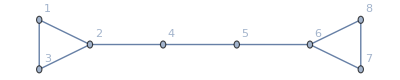

0

-Graphics3D-

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
s = simplifyGraph[g];
GraphPlot3D[s]
```

test mergeScore

```mathematica
ball1 = {{1,2,3},2};
ball2 = {{4,5,6},6};
mergeScore[ball1, ball2]
```

Part::partw: Part 3 of {{1,2,3},2} does not exist.

Part::partw: Part 3 of {{4,5,6},6} does not exist.

Part::partw: Part 3 of {{1,2,3},2} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(-4+Max[{{1,2,3},2}⟦3⟧,{{4,5,6},6}⟦3⟧]+Min[{{1,2,3},2}⟦3⟧,{{4,5,6},6}⟦3⟧])/(2 Min[{{1,2,3},2}⟦3⟧,{{4,5,6},6}⟦3⟧])

test simplifyGraph

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
h = simplifyGraph[g];
GraphPlot3D[h]
```

-Graphics-

0

-Graphics3D-

test smallestCircumBall

```mathematica
c1 = {0,0,0};
r1 = 1;
c2 = {0.1,0.5,0.6};
r2 = 0.4;
{c3,r3} = smallestCircumBall[{1,2,c1,r1},{1,2,c2,r2}]

a1 = Ball[c1,r1];
a2 = Ball[c2,r2];
a3 = Ball[c3,r3];

Graphics3D[{
	Opacity[0.5],
	Green,a1,
	Blue,a2,
	Red,a3}]
```

Part::partw: Part 5 of {1,2,{0,0,0},1} does not exist.

Part::partw: Part 5 of {1,2,{0.1,0.5,0.6},0.4} does not exist.

{1-0.3 (Max[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]+Min[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]),0.3 (Abs[Max[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]]+Abs[Min[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]])}

-Graphics3D-

## Code

### Set working directory

```mathematica
SetDirectory["D:\\MyLearning\\proj\\Skeleton_Analysis_of_Melt_Network"];
```

### Excel Data

```mathematica
groundTruthTable = Import["data\\scoba12.xlsx"];
```

```mathematica
groundTruthTable = groundTruthTable[[1,;;,;;]];
trueJunctions = groundTruthTable[[;;,{4,5,6,10,19}]];
```

### Processing data of scoba12_small

#### Median Axes

```mathematica
maRawData = Import["data\\scoba12_small.ply","Table"];
maTable = maRawData⟦15;;,;;⟧;
maPoints = maTable⟦;;86117,;;⟧;
maPoints = coordsAlign[maPoints,skelPoints];
maPolygons = maTable⟦363203;;,10;;12⟧ + 1;
```

```mathematica
polygonInCoords = Table[{Blue,Polygon[{maPoints⟦maPolygon⟦1⟧⟧,maPoints⟦maPolygon⟦2⟧⟧,maPoints⟦maPolygon⟦3⟧⟧}]},{maPolygon,maPolygons}];
```

#### Skeleton data

```mathematica
{skelPoints,skelLines,skelRadius} = readSkel["data\\scoba12_small_skel_0.1.ply"];
```

```mathematica
{J,G}=initJG[skelPoints,skelLines,skelRadius];
```

```mathematica
{Jres,Gres}=computeCN[J,G];
```

```mathematica
junctionBalls = Table[{Ball[skelPoints⟦junctions⟦i,1⟧,;;⟧,skelRadius⟦junctions⟦i,1⟧⟧]},{i,Dimensions[junctions]⟦1⟧}];
```

### Cube1

```mathematica
{points1,lines1,radius1} = readSkel["data\\cube1\\cube1_skel.ply"];
```

```mathematica
{J1,G1}=initJG[points1,lines1,radius1];
```

```mathematica
Export["basicJunctions1.xls", J1, "XLS"];
adjMatrix1 = AdjacencyMatrix[G1];
Export["adjMatrix1.xls", adjMatrix1, "XLS"];
```

```mathematica
J1 = Import["data\\cube1\\basicJunctions1.xls"]⟦1⟧;
G1 = Import["data\\cube1\\simplifiedG1.gv"];
```

```mathematica
{Jres1,Gres1}=computeCN[J1,G1];
```

```mathematica
Export["mergedJunctions1.xls", Jres1, "XLS"];
adjMatrixRes1 = AdjacencyMatrix[Gres1];
Export["adjMatrixRes1.xls", adjMatrixRes1, "XLS"];
```

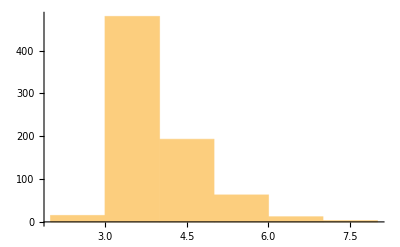

```mathematica
CNs = Jres1⟦;;,2⟧;
Histogram[CNs]
```

### Cube2

```mathematica
{points2,lines2,radius2} = readSkel["data\\cube2\\cube2_skel.ply"];
```

```mathematica
{J2,G2}=initJG[points2,lines2,radius2];
```

Initial graph built!

Basic junctions computed!

47500

47000

46500

46000

45500

45000

44500

44000

43500

43000

42500

42000

41500

41000

40500

40000

```mathematica
Export["basicJunctions2.xls", J2, "XLS"];
adjMatrix2 = AdjacencyMatrix[G2];
Export["adjMatrix2.xls",adjMatrix2,"XLS"];
```

```mathematica
{Jres2,Gres2}=computeCN[J2,G2];
```

```mathematica
Export["mergedJunctions2.xls", Jres2, "XLS"];
adjMatrixRes2 = AdjacencyMatrix[Gres2];
Export["adjMatrixRes2.xls",adjMatrixRes2,"XLS"];
```

```mathematica
CNs = Jres1⟦;;,2⟧;
Histogram[CNs]
```

### Cube3

```mathematica
{points3,lines3,radius3} = readSkel["data\\cube3\\cube3_skel.ply"];
```

```mathematica
{J3,G3}=initJG[points3,lines3,radius3];
```

```mathematica
Export["basicJunctions3.xls", J3, "XLS"];
adjMatrix3 = AdjacencyMatrix[G3];
Export["adjMatrix3.xls",adjMatrix3,"XLS"];
```

```mathematica
{Jres3,Gres3}=computeCN[J3,G3];
```

```mathematica
Export["mergedJunctions3.xls", Jres3, "XLS"];
adjMatrixRes3 = AdjacencyMatrix[Gres3];
Export["adjMatrixRes3.xls",adjMatrixRes3,"XLS"];
```

```mathematica
CNs = Jres1⟦;;,2⟧;
Histogram[CNs]
```

### Cube4

```mathematica
{points4,lines4,radius4} = readSkel["data\\cube4\\cube4_skel.ply"];
```

```mathematica
{J4,G4}=initJG[points4,lines4,radius4];
```

```mathematica
Export["basicJunctions4.xls", J4, "XLS"];
adjMatrix4 = AdjacencyMatrix[G4];
Export["adjMatrix4.xls",adjMatrix4,"XLS"];
```

```mathematica
{Jres4,Gres4}=computeCN[J4,G4];
```

```mathematica
Export["mergedJunctions4.xls", Jres4, "XLS"];
adjMatrixRes4 = AdjacencyMatrix[Gres4];
Export["adjMatrixRes4.xls",adjMatrixRes4,"XLS"];
```

```mathematica
CNs = Jres1⟦;;,2⟧;
Histogram[CNs]
```

### Cube2-4

```mathematica
{points2,lines2,radius2} = readSkel["data\\cube2\\cube2_skel.ply"];
{J2,G2}=initJG[points2,lines2,radius2];
Export["basicJunctions2.xls", J2, "XLS"];
adjMatrix2 = AdjacencyMatrix[G2];
Export["simplifiedG2.gv",adjMatrix2,"DOT"];
{Jres2,Gres2}=computeCN[J2,G2];
Export["mergedJunctions2.xls", Jres2, "XLS"];
adjMatrixRes2 = AdjacencyMatrix[Gres2];
Export["mergedG2.gv",adjMatrixRes2,"DOT"];

{points3,lines3,radius3} = readSkel["data\\cube3\\cube3_skel.ply"];
{J3,G3}=initJG[points3,lines3,radius3];
Export["basicJunctions3.xls", J3, "XLS"];
adjMatrix3 = AdjacencyMatrix[G3];
Export["simplifiedG3.gv",adjMatrix3,"DOT"];
{Jres3,Gres3}=computeCN[J3,G3];
Export["mergedJunctions3.xls", Jres3, "XLS"];
adjMatrixRes3 = AdjacencyMatrix[Gres3];
Export["mergedG3.gv",adjMatrixRes3,"DOT"];

{points4,lines4,radius4} = readSkel["data\\cube4\\cube4_skel.ply"];
{J4,G4}=initJG[points4,lines4,radius4];
Export["basicJunctions4.xls", J4, "XLS"];
adjMatrix4 = AdjacencyMatrix[G4];
Export["simplifiedG4.gv",adjMatrix4,"DOT"];
{Jres4,Gres4}=computeCN[J4,G4];
Export["mergedJunctions4.xls", Jres4, "XLS"];
adjMatrixRes4 = AdjacencyMatrix[Gres4];
Export["mergedG4.gv",adjMatrixRes4,"DOT"];
```

Initial graph built!

Basic junctions computed!

simplified graph done!

Power::infy: Infinite expression 1/0 encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Initial graph built!

Basic junctions computed!

simplified graph done!

Power::infy: Infinite expression 1/0 encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

$Aborted

Initial graph built!

Basic junctions computed!

$Aborted

```mathematica
CNs = Jres1⟦;;,2⟧;
Histogram[CNs]
```

## Real-World Data Test & Visualization

validate visualization of median axes

```mathematica
maGraphic = Import["data\\scoba12_small.ply","Graphics3D"];
(*Show[Graphics3D[polygonInCoords],maGraphic]*)
```

validate visualization of skeleton

```mathematica
edgeInCoords = Table[{Opacity[0.5],Green,Thickness[0.004],Line[{skelPoints⟦skelLine⟦1⟧⟧,skelPoints⟦skelLine⟦2⟧⟧}]},{skelLine,skelLines}];
```

```mathematica
skelGraphic = Import["data\\scoba12_small_skel_0.1.ply","Graphics3D"];

Show[Graphics3D[edgeInCoords],skelGraphic]
```

show junction balls in median axes

```mathematica
Show[Graphics3D[{edgeInCoords,{Opacity[1],Blue,junctionBalls}}], maGraphic]
Show[Graphics3D[{edgeInCoords,{Opacity[0.5],Blue,junctionBalls}}]]
```

-Graphics3D-

```mathematica
simplifiedG = simplifyGraph[skelGraph];
GraphPlot3D[simplifiedG]
```

-Graphics3D-

```mathematica
{J2,G2}=computeCN[junctionsDataTable,simplifiedG];
```

{1.92489,342}

{1.84845,341}

{1.62726,340}

{1.57805,339}

{1.50871,338}

{1.44328,337}

{1.42878,336}

{1.36439,335}

{1.31305,334}

{1.14462,333}

{1.12584,332}

{1.09765,331}

{1.08843,330}

{1.08678,329}

{1.07687,328}

{1.05684,327}

{1.04245,326}

{1.04079,325}

{1.03049,324}

{1.01204,323}

{0.989383,322}

{0.989243,321}

{0.954593,320}

{0.95152,319}

{0.948493,318}

{0.943107,317}

{0.931016,316}

{0.925381,315}

{0.895799,314}

{0.894749,313}

{0.879033,312}

{0.877954,311}

{0.867431,310}

{0.867145,309}

{0.857482,308}

{0.846551,307}

{0.833837,306}

{0.82912,305}

{0.822867,304}

{0.818381,303}

{0.769183,302}

{0.76118,301}

{0.7584,300}

{0.748819,299}

{0.744387,298}

{0.712621,297}

{0.707889,296}

{0.688131,295}

{0.68492,294}

{0.677182,293}

{0.642407,292}

{0.632139,291}

{0.629725,290}

{0.625462,289}

{0.624622,288}

{0.624091,287}

{0.607708,286}

{0.581264,285}

{0.57741,284}

{0.576734,283}

{0.56966,282}

{0.56435,281}

{0.558934,280}

{0.543526,279}

{0.531915,278}

{0.529943,277}

{0.517552,276}

{0.515725,275}

{0.509481,274}

{0.509379,273}

{0.504352,272}

{0.470422,271}

{0.454182,270}

{0.449651,269}

{0.443022,268}

{0.42251,267}

{0.400023,266}

{0.383337,265}

{0.381039,264}

{0.373067,263}

{0.372065,262}

{0.338807,261}

{0.30864,260}

{0.307442,259}

{0.305966,258}

{0.303838,257}

{0.293098,256}

{0.29179,255}

{0.285655,254}

{0.284853,253}

{0.28484,252}

{0.283883,251}

{0.283226,250}

{0.27919,249}

{0.25625,248}

{0.251548,247}

{0.242061,246}

{0.223381,245}

{0.190623,244}

{0.189458,243}

{0.187133,242}

{0.181346,241}

{0.165495,240}

{0.161173,239}

{0.14851,238}

{0.145028,237}

{0.11482,236}

{0.102181,235}

{0.0925174,234}

{0.0843705,233}

{0.0835335,232}

{0.0790402,231}

{0.0695585,230}

{0.0573527,229}

{0.0384913,228}

{0.0363785,227}

{0.0239849,226}

{0.00973067,225}

{0.00705329,224}

```mathematica
mergedJunctionBalls = Table[{Ball[J2⟦i,4⟧,J2⟦i,5⟧]},{i,Dimensions[J2]⟦1⟧}];
```

```mathematica
Show[Graphics3D[{
	edgeInCoords,
	Opacity[0.5],Red,junctionBalls,
	Opacity[0.3],Blue,mergedJunctionBalls
}]]
```

-Graphics3D-

{3,3,5,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,2,4,4,4,4,4,4,4,4,4,4,4,4,5,4,4,4,4,4,4,3,4,4,4,4,4,5,4,4,4,3,2,4,4,4,4,5,2,4,4,4,4,5,4,4,4,5,7,5,4,5,4,4,6,7,5,2,5,4,4,4,6,4,4,5,4,4,5,5,4,6,4,4,4,4,5,6,4,6,4,7,6}

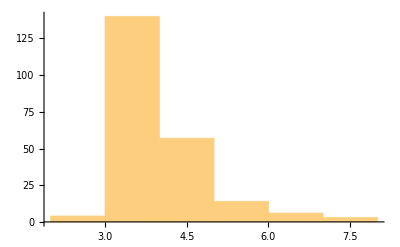

```mathematica
CNs = J2⟦;;,2⟧
Histogram[CNs]
```

Test correctness of the simplified graph

```mathematica
list = VertexList[G];
nodesDeg1 = Pick[VertexList[G], VertexDegree[G], 1];
Length[list] - Length[nodesDeg1]
```

157

```mathematica
simplifiedJ = DeleteCases[list, Alternatives @@ nodesDeg1];
trueJ = junctionsDataTable⟦;;,1⟧;

For[i = 1, i ≤ Length[trueJ], i++,
	If[!MemberQ[trueJ,simplifiedJ⟦i⟧],Print[False]];
]
```

```mathematica
Sort[simplifiedJ]
Sort[trueJ]
```

{2,52,117,134,158,161,172,203,215,223,230,231,246,271,300,358,376,429,439,442,457,506,534,547,595,633,684,712,715,723,775,818,846,854,865,885,890,893,899,901,908,914,946,960,973,1056,1103,1156,1179,1248,1252,1283,1302,1309,1310,1314,1318,1332,1346,1347,1349,1383,1391,1410,1415,1438,1465,1467,1490,1564,1574,1584,1601,1602,1668,1717,1726,1729,1814,1817,1841,1924,1990,2005,2023,2041,2087,2106,2121,2134,2168,2199,2205,2209,2250,2251,2254,2291,2364,2441,2502,2569,2581,2588,2645,2652,2666,2671,2678,2699,2702,2707,2714,2726,2741,2747,2757,2767,2772,2775,2778,2780,2781,2783,2787,2788,2846,2866,2868,2869,2985,2989,3055,3111,3117,3132,3174,3188,3220,3382,3384,3418,3426,3454,3498,3522,3643,3707,3773,3809,3815,3820,3822,3828,3884,3903,3969,3999,4099,4117,4205,4232,4291,4308,4360,4420,4440,4455,4487,4495,4564,4573,4597,4601,4619,4661,4795,4812,4816,4830,4845,4882,4884,4887,4935,4952,4962,4988,5099,5100,5181,5189,5206,5241,5311,5317,5324,5358,5359,5374,5382,5423,5525,5568,5582,5586,5596,5702,5710,5735,5786,5796,5832,5859,5873,5879,5890,5893,5908,5910,5919,6018,6068,6079,6135,6172,6181,6196,6281,6413,6448,6452,6478,6512,6525,6539,6548,6743,6883,6910,6921,6952,6978,7012,7041,7068,7080,7114,7129,7173,7230,7240,7263,7284,7304,7386,7482,7591,7606,7624,7685,7716,7720,7741,7782,7801,7825,7833,7844,7860,7926,8040,8139,8150,8151,8219,8222,8327,8350,8485,8536,8599,8609,8667,8721,8727,8871,9019,9148,9200,9211,9414,9695,9784,9862,9887,9907,9912,9918,9947,9949,9953,9957,9967,9986,10044,10152,10235,10274,10365,10436,10494,10514,10562,10633,10679,10696,10861,10921,10944,11045,11165,11249,11328,11362,11369,11395,11571,11577,11752,11800,11801,11876,11897,11930,11998,12021,12023,12056,12139,12173,12187,12250}

{2,52,117,134,158,161,172,203,215,223,230,231,246,271,300,358,376,429,439,442,457,506,534,547,595,633,684,712,715,723,775,818,846,854,865,885,890,893,899,901,908,914,946,960,973,1056,1103,1156,1179,1248,1252,1283,1302,1309,1310,1314,1318,1332,1346,1347,1349,1383,1391,1410,1415,1438,1465,1467,1490,1564,1574,1584,1601,1602,1668,1717,1726,1729,1814,1817,1841,1924,1990,2005,2023,2041,2087,2106,2121,2134,2168,2199,2205,2209,2250,2251,2254,2291,2364,2441,2502,2569,2581,2588,2645,2652,2666,2671,2678,2699,2702,2707,2714,2726,2741,2747,2757,2767,2772,2775,2778,2780,2781,2783,2787,2788,2846,2866,2868,2869,2985,2989,3055,3111,3117,3132,3174,3188,3220,3382,3384,3418,3426,3454,3498,3522,3643,3707,3773,3809,3815,3820,3822,3828,3884,3903,3969,3999,4099,4117,4205,4232,4291,4308,4360,4420,4440,4455,4487,4495,4564,4573,4597,4601,4619,4661,4795,4812,4816,4830,4845,4882,4884,4887,4935,4952,4962,4988,5099,5100,5181,5189,5206,5241,5311,5317,5324,5358,5359,5374,5382,5423,5525,5568,5582,5586,5596,5702,5710,5735,5786,5796,5832,5859,5873,5879,5890,5893,5908,5910,5919,6018,6068,6079,6135,6172,6181,6196,6281,6413,6448,6452,6478,6512,6525,6539,6548,6743,6883,6910,6921,6952,6978,7012,7041,7068,7080,7114,7129,7173,7230,7240,7263,7284,7304,7386,7482,7591,7606,7624,7685,7716,7720,7741,7782,7801,7825,7833,7844,7860,7926,8040,8139,8150,8151,8219,8222,8327,8350,8485,8536,8599,8609,8667,8721,8727,8871,9019,9148,9200,9211,9414,9695,9784,9862,9887,9907,9912,9918,9947,9949,9953,9957,9967,9986,10044,10152,10235,10274,10365,10436,10494,10514,10562,10633,10679,10696,10861,10921,10944,11045,11165,11249,11328,11362,11369,11395,11571,11577,11752,11800,11801,11876,11897,11930,11998,12021,12023,12056,12139,12173,12187,12250}